# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Washington"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
startDate="2021-11-01";
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-13

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-13

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Wisconsin}

```mathematica
Length[states]
```

34

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

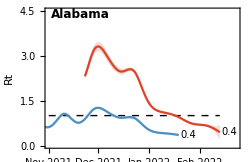
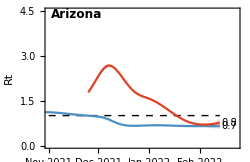
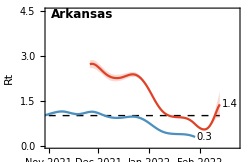
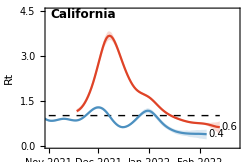
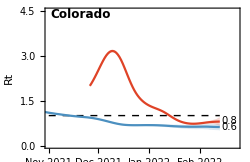
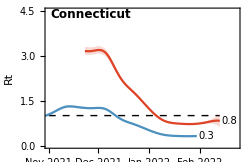
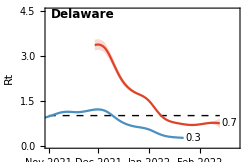
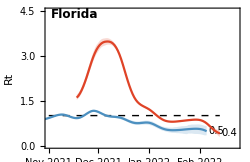
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Alabama→{2022-02-13,0.4,0.2,0.7},Arizona→{2022-02-13,0.8,0.6,0.9},Arkansas→{2022-02-13,1.4,0.9,1.8},California→{2022-02-13,0.6,0.4,0.8},Colorado→{2022-02-13,0.8,0.6,0.9},Connecticut→{2022-02-13,0.8,0.6,1.},Delaware→{2022-02-13,0.7,0.6,0.9},Florida→{2022-02-13,0.4,0.3,0.5},Georgia→{2022-02-13,0.7,0.5,0.9},Illinois→{2022-02-13,0.7,0.6,1.},Indiana→{2022-02-13,0.9,0.6,1.2},Louisiana→{2022-02-13,0.7,0.5,0.9},Maryland→{2022-02-13,0.9,0.7,1.},Massachusetts→{2022-02-13,0.8,0.6,1.},Michigan→{2022-02-13,0.7,0.5,0.9},Minnesota→{2022-02-13,0.8,0.6,1.},Nebraska→{2022-02-13,0.5,0.4,0.6},Nevada→{2022-02-13,0.7,0.5,0.9},New Hampshire→{2022-02-13,1.,0.7,1.3},New Jersey→{2022-02-13,0.8,0.7,0.9},New Mexico→{2022-02-13,0.7,0.4,0.9},New York→{2022-02-13,0.8,0.6,0.9},North Carolina→{2022-02-13,1.,0.8,1.2},North Dakota→{2022-02-13,0.7,0.6,0.9},Ohio→{2022-02-13,0.7,0.6,0.8},Oregon→{2022-02-13,0.8,0.6,0.9},Pennsylvania→{2022-02-13,0.7,0.6,0.8},South Carolina→{2022-02-13,0.7,0.6,0.9},Tennessee→{2022-02-13,0.8,0.6,0.9},Texas→{2022-02-13,0.8,0.6,1.},Utah→{2022-02-13,0.8,0.6,1.},Vermont→{2022-02-13,0.8,0.6,1.},Virginia→{2022-02-13,0.8,0.7,0.9},Wisconsin→{2022-02-13,0.8,0.6,0.9}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

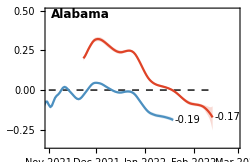
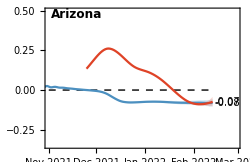
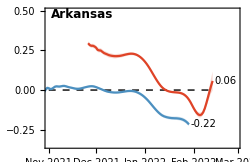
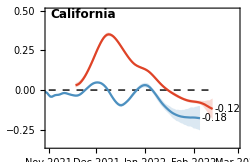
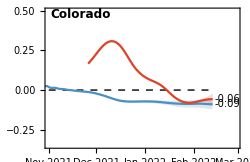
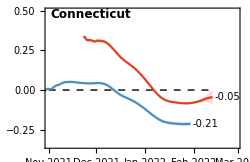
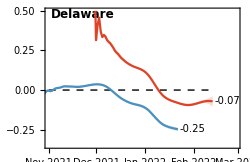
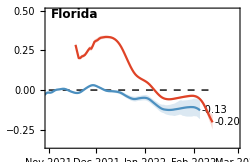
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Alabama→{2022-02-13,-0.17,-0.25,-0.1},Arizona→{2022-02-13,-0.07,-0.1,-0.04},Arkansas→{2022-02-13,0.06,0.,0.12},California→{2022-02-13,-0.12,-0.19,-0.05},Colorado→{2022-02-13,-0.06,-0.09,-0.02},Connecticut→{2022-02-13,-0.05,-0.09,0.},Delaware→{2022-02-13,-0.07,-0.11,-0.04},Florida→{2022-02-13,-0.2,-0.25,-0.16},Georgia→{2022-02-13,-0.09,-0.14,-0.03},Illinois→{2022-02-13,-0.08,-0.12,-0.03},Indiana→{2022-02-13,-0.03,-0.09,0.03},Louisiana→{2022-02-13,-0.08,-0.13,-0.04},Maryland→{2022-02-13,-0.04,-0.07,-0.02},Massachusetts→{2022-02-13,-0.06,-0.1,-0.02},Michigan→{2022-02-13,-0.09,-0.14,-0.04},Minnesota→{2022-02-13,-0.05,-0.09,0.},Nebraska→{2022-02-13,-0.17,-0.2,-0.13},Nevada→{2022-02-13,-0.09,-0.13,-0.04},New Hampshire→{2022-02-13,0.,-0.05,0.06},New Jersey→{2022-02-13,-0.05,-0.08,-0.03},New Mexico→{2022-02-13,-0.09,-0.15,-0.03},New York→{2022-02-13,-0.06,-0.09,-0.03},North Carolina→{2022-02-13,-0.01,-0.05,0.03},North Dakota→{2022-02-13,-0.07,-0.1,-0.05},Ohio→{2022-02-13,-0.08,-0.12,-0.06},Oregon→{2022-02-13,-0.07,-0.11,-0.04},Pennsylvania→{2022-02-13,-0.1,-0.12,-0.07},South Carolina→{2022-02-13,-0.08,-0.12,-0.03},Tennessee→{2022-02-13,-0.07,-0.11,-0.03},Texas→{2022-02-13,-0.07,-0.11,-0.03},Utah→{2022-02-13,-0.07,-0.11,-0.02},Vermont→{2022-02-13,-0.06,-0.11,-0.01},Virginia→{2022-02-13,-0.06,-0.09,-0.02},Wisconsin→{2022-02-13,-0.07,-0.12,-0.03}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Alabama→{2022-02-13,-4.,-6.7,-2.7},Arizona→{2022-02-13,-9.4,-16.,-6.7},Arkansas→{2022-02-13,12.,5.9,-194.5},California→{2022-02-13,-5.8,-13.,-3.7},Colorado→{2022-02-13,-12.2,-31.3,-7.6},Connecticut→{2022-02-13,-15.3,298.7,-7.4},Delaware→{2022-02-13,-9.8,-18.2,-6.5},Florida→{2022-02-13,-3.4,-4.4,-2.8},Georgia→{2022-02-13,-8.,-21.9,-5.},Illinois→{2022-02-13,-9.,-23.9,-5.6},Indiana→{2022-02-13,-21.7,20.5,-7.4},Louisiana→{2022-02-13,-8.6,-17.,-5.5},Maryland→{2022-02-13,-16.4,-39.5,-9.7},Massachusetts→{2022-02-13,-11.1,-37.8,-7.1},Michigan→{2022-02-13,-7.5,-15.8,-5.1},Minnesota→{2022-02-13,-14.7,-209.1,-8.},Nebraska→{2022-02-13,-4.1,-5.2,-3.4},Nevada→{2022-02-13,-8.,-17.5,-5.3},New Hampshire→{2022-02-13,205.5,11.6,-12.8},New Jersey→{2022-02-13,-13.3,-27.,-9.},New Mexico→{2022-02-13,-7.5,-20.6,-4.6},New York→{2022-02-13,-11.,-21.1,-7.6},North Carolina→{2022-02-13,-49.3,22.5,-13.3},North Dakota→{2022-02-13,-9.3,-14.9,-6.7},Ohio→{2022-02-13,-8.2,-12.,-6.},Oregon→{2022-02-13,-9.5,-16.8,-6.6},Pennsylvania→{2022-02-13,-7.2,-9.6,-5.8},South Carolina→{2022-02-13,-8.9,-23.1,-5.7},Tennessee→{2022-02-13,-9.4,-21.,-6.3},Texas→{2022-02-13,-10.,-27.7,-6.3},Utah→{2022-02-13,-9.8,-27.9,-6.2},Vermont→{2022-02-13,-11.3,-75.5,-6.3},Virginia→{2022-02-13,-12.5,-29.8,-8.1},Wisconsin→{2022-02-13,-9.4,-25.6,-5.9}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

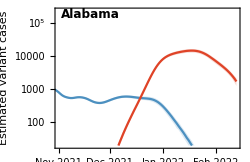
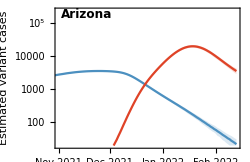
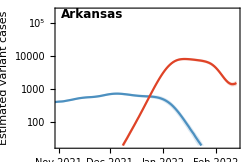
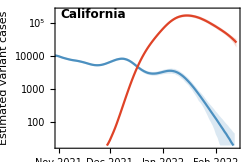
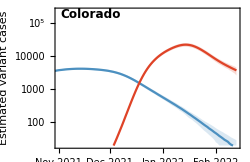
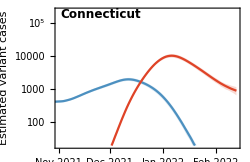
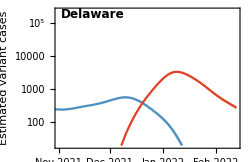
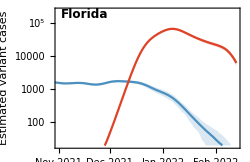
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

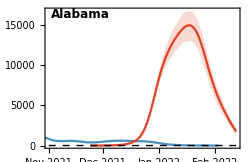
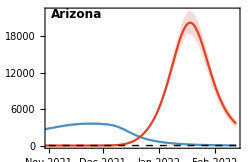
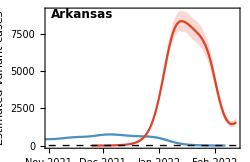
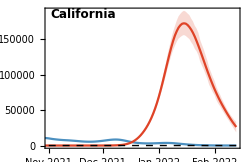
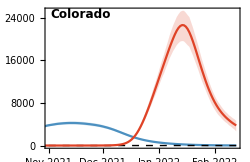
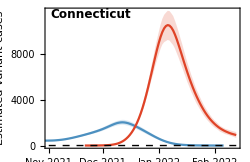
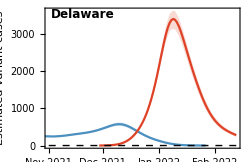
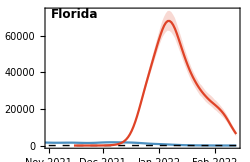
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Alabama→{2022-02-13,1742,1271,2202},Arizona→{2022-02-13,3597,2919,4301},Arkansas→{2022-02-13,1560,1254,1868},California→{2022-02-13,26230,18641,33426},Colorado→{2022-02-13,3765,2642,4620},Connecticut→{2022-02-13,913,659,1179},Delaware→{2022-02-13,279,230,327},Florida→{2022-02-13,6322,4939,7666},Georgia→{2022-02-13,3484,2862,4149},Illinois→{2022-02-13,4223,3283,5146},Indiana→{2022-02-13,3622,2799,4438},Louisiana→{2022-02-13,2535,1907,3284},Maryland→{2022-02-13,805,643,954},Massachusetts→{2022-02-13,1306,864,1668},Michigan→{2022-02-13,2717,2152,3314},Minnesota→{2022-02-13,3448,2825,4030},Nebraska→{2022-02-13,268,179,361},Nevada→{2022-02-13,996,790,1202},New Hampshire→{2022-02-13,1040,723,1328},New Jersey→{2022-02-13,1749,1379,2044},New Mexico→{2022-02-13,1524,1011,1903},New York→{2022-02-13,4792,3492,5917},North Carolina→{2022-02-13,5960,4688,7220},North Dakota→{2022-02-13,629,502,796},Ohio→{2022-02-13,2046,1750,2313},Oregon→{2022-02-13,2289,1269,3338},Pennsylvania→{2022-02-13,3225,2752,3627},South Carolina→{2022-02-13,2002,1528,2410},Tennessee→{2022-02-13,3397,2802,4002},Texas→{2022-02-13,12537,9632,15203},Utah→{2022-02-13,1765,1392,2124},Vermont→{2022-02-13,574,364,761},Virginia→{2022-02-13,4805,3833,5690},Wisconsin→{2022-02-13,2244,1752,2725}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Alabama→{2022-02-13,1.,1.,1.},Arizona→{2022-02-13,0.99,0.99,1.},Arkansas→{2022-02-13,1.,1.,1.},California→{2022-02-13,1.,1.,1.},Colorado→{2022-02-13,0.99,0.99,1.},Connecticut→{2022-02-13,1.,1.,1.},Delaware→{2022-02-13,1.,1.,1.},Florida→{2022-02-13,1.,1.,1.},Georgia→{2022-02-13,1.,1.,1.},Illinois→{2022-02-13,1.,0.99,1.},Indiana→{2022-02-13,1.,1.,1.},Louisiana→{2022-02-13,1.,1.,1.},Maryland→{2022-02-13,1.,0.99,1.},Massachusetts→{2022-02-13,1.,1.,1.},Michigan→{2022-02-13,1.,0.99,1.},Minnesota→{2022-02-13,1.,1.,1.},Nebraska→{2022-02-13,0.82,0.75,0.9},Nevada→{2022-02-13,1.,1.,1.},New Hampshire→{2022-02-13,1.,1.,1.},New Jersey→{2022-02-13,1.,1.,1.},New Mexico→{2022-02-13,1.,1.,1.},New York→{2022-02-13,1.,1.,1.},North Carolina→{2022-02-13,1.,1.,1.},North Dakota→{2022-02-13,1.,1.,1.},Ohio→{2022-02-13,1.,1.,1.},Oregon→{2022-02-13,0.97,0.95,0.98},Pennsylvania→{2022-02-13,0.94,0.92,0.96},South Carolina→{2022-02-13,1.,1.,1.},Tennessee→{2022-02-13,1.,0.99,1.},Texas→{2022-02-13,1.,1.,1.},Utah→{2022-02-13,1.,1.,1.},Vermont→{2022-02-13,1.,1.,1.},Virginia→{2022-02-13,1.,1.,1.},Wisconsin→{2022-02-13,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,650},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]],Prolog->{Dashed,Black,Line[{{0,0},{1000,0}}]}];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png

### Growth rate vs peak incidence

```mathematica
initialR[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,(#1[[1]]-10)^2<(#2[[1]]-10)^2&];
sorted[[1,2]]
]
```

```mathematica
initialR["Washington","Omicron"]
```

0.186846

```mathematica
peakIncidence[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,#1[[1]]>#2[[1]]&];
sorted[[1,1]]
]
```

```mathematica
peakIncidence["Washington","Omicron"]
```

501.52

```mathematica
pairs=Map[{initialR[#,"Omicron"],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Initial epidemic growth rate r","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
rValues=Map[initialR[#,"Omicron"]&,states]
```

{0.240289,0.208117,0.226609,0.288957,0.292237,0.25793,0.248071,0.320288,0.243026,0.240186,0.197173,0.164683,0.246668,0.271135,0.227839,0.167856,0.208524,0.211524,0.217434,0.26454,0.19353,0.270498,0.245187,0.162978,0.20986,0.222018,0.199705,0.192941,0.185286,0.184516,0.232032,0.172175,0.247843,0.215257}

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.15],0.0],Lighter[ColorData["Rainbow"][0.3],0.0],Lighter[ColorData["Rainbow"][0.7],0.0],Lighter[ColorData["Rainbow"][0.9],0.0]},t]
```

```mathematica
standardizedColorFunction[t_,min_,max_]:=baseColorFunction[(t-min)/(max-min)]
```

```mathematica
phaseColors=Map[standardizedColorFunction[#,Min[rValues],Max[rValues]]&,rValues]
```

{RGBColor[0.5400740134523825, 0.6347142558483393, 0.5168221309290799],RGBColor[0.2910166770851836, 0.5259833947013635, 0.7572047768446833],RGBColor[0.4069175441198509, 0.5968092935160254, 0.6462949095101866],RGBColor[0.8423979367174893, 0.5817109559571376, 0.22515484018520684],RGBColor[0.8476908934394375, 0.5616046264733484, 0.22036468714046756],RGBColor[0.7117757458022284, 0.6835916985271523, 0.3498704200136506],RGBColor[0.615814039568156, 0.6562747767254534, 0.44317740544056033],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.566709959851943, 0.6422965727272849, 0.4909230513892323],RGBColor[0.5390691441794278, 0.6344282049179475, 0.5177992011197541],RGBColor[0.28060386736531473, 0.4662783155118446, 0.7646529157846318],RGBColor[0.24969051115064675, 0.28902698465454696, 0.7867648124178364],RGBColor[0.6021572003887365, 0.6523871550629895, 0.45645643667395125],RGBColor[0.8136406078254635, 0.6909512842181144, 0.25118037067547017],RGBColor[0.4188918794003643, 0.6002179655094895, 0.6346518367537428],RGBColor[0.2527102471867788, 0.30634157927588995, 0.7846048369487596],RGBColor[0.29140321380183387, 0.5281997230409881, 0.7569282924712573],RGBColor[0.29425735920594254, 0.5445648523341464, 0.7548867616936369],RGBColor[0.31761363215240673, 0.57138761151873, 0.7331282844002396],RGBColor[0.7761146326030469, 0.7019067161369817, 0.28731142842523266],RGBColor[0.2771376912214028, 0.4464039178493, 0.7671322236952459],RGBColor[0.8126126302239793, 0.6948562578355425, 0.2521106956897017],RGBColor[0.5877415505882447, 0.6482835267119037, 0.4704732865054138],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2926744482505033, 0.5354887406518091, 0.7560189960321921],RGBColor[0.36222733613842706, 0.5840875635193493, 0.6897487907352341],RGBColor[0.28301226722129297, 0.480087624237311, 0.7629302206396269],RGBColor[0.2765773909037043, 0.44319126192471614, 0.7675329987719626],RGBColor[0.2692936675494231, 0.4014277714393273, 0.7727429454628464],RGBColor[0.2685609546919122, 0.3972265346590763, 0.7732670448474165],RGBColor[0.4597020889482539, 0.611835196451709, 0.5949706162232764],RGBColor[0.25681930013053883, 0.32990211077518306, 0.781665688144539],RGBColor[0.6135931850349308, 0.6556425775702083, 0.44533682141698594],RGBColor[0.29780950851412497, 0.5649322038409498, 0.7523459583663368]}

```mathematica
Min[rValues]
```

0.162978

```mathematica
Max[rValues]
```

0.320288

```mathematica
legend=PointLegend[Table[standardizedColorFunction[i,Min[rValues],Max[rValues]],{i,0.15,0.3,0.05}],Table["initial r = "<>ToString[NumberForm[Round[i,0.01],{3,2}]],{i,0.15,0.3,0.05}],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{3,600},
{-0.25,0.4}},PlotStyle->Map[Directive[#,Opacity[0.5]]&,phaseColors],PlotLegends->Placed[legend,Right]]
```

-Graphics-

```mathematica
figPoints=ListLogLinearPlot[Map[{#}&,statePoints],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->phaseColors,PlotMarkers->{"•",Scaled[0.1]}]
```

-Graphics-

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

### Mapping

```mathematica
mapFig=Module[{entities},
GeoGraphics[{Map[{GeoStyling[Opacity@1,EdgeForm[GrayLevel[0.8]],FaceForm[GrayLevel[0.9]]],Polygon@#}&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]]},GeoRangePadding->None,GeoRange->{{25,49},{-125,-67}},GeoBackground->None,ImageSize->400,ImageMargins->0]
]
```

-Graphics-

```mathematica
fullStateNamesToAbbreviations={"Alaska"->"AK","Washington"->"WA","Idaho"->"ID","Montana"->"MT","Oregon"->"OR","Nevada"->"NV","Wyoming"->"WY","California"->"CA","Utah"->"UT","Colorado"->"CO","Hawaii"->"HI","Arizona"->"AZ","New Mexico"->"NM","Oklahoma"->"OK","Texas"->"TX","North Dakota"->"ND","Minnesota"->"MN","Illinois"->"IL","Wisconsin"->"WI","Michigan"->"MI","South Dakota"->"SD","Iowa"->"IA","Indiana"->"IN","Ohio"->"OH","Nebraska"->"NE","Missouri"->"MO","Kansas"->"KS","Kentucky"->"KY","West Virginia"->"WV","Virginia"->"VA","Arkansas"->"AR","Tennessee"->"TN","North Carolina"->"NC","South Carolina"->"SC","Louisiana"->"LA","Mississippi"->"MS","Alabama"->"AL","Georgia"-> "GA","Florida"->"FL","Maine"->"ME","Vermont"->"VT","New Hampshire"->"NH","New York"->"NY","Massachusetts"->"MA","Rhode Island"->"RI","Pennsylvania"->"PA","New Jersey"->"NJ","Connecticut"-> "CT","Maryland"->"MD","Washington DC"->"DC","Delaware"->"DE"};
```

```mathematica
abbreviationsToFullStateNames=Map[#[[2]]->#[[1]]&,fullStateNamesToAbbreviations];
```

```mathematica
geoCasesPerCapita=DeleteCases[Map[#->With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],peakIncidence[state,"Omicron"],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x[[2]]==Null]
```

{Alabama, United States→297.094,Arizona, United States→282.347,Arkansas, United States→276.532,California, United States→436.825,Colorado, United States→390.995,Connecticut, United States→290.469,Delaware, United States→344.759,Florida, United States→315.829,Georgia, United States→224.964,Illinois, United States→288.456,Indiana, United States→261.506,Louisiana, United States→426.69,Maryland, United States→213.895,Massachusetts, United States→276.706,Michigan, United States→243.732,Minnesota, United States→289.522,Nebraska, United States→209.643,Nevada, United States→310.25,New Hampshire, United States→402.585,New Jersey, United States→352.8,New Mexico, United States→525.417,New York, United States→390.621,North Carolina, United States→306.152,North Dakota, United States→338.847,Ohio, United States→207.853,Oregon, United States→265.779,Pennsylvania, United States→203.053,South Carolina, United States→292.524,Tennessee, United States→230.334,Texas, United States→237.358,Utah, United States→639.951,Vermont, United States→450.037,Virginia, United States→292.101,Wisconsin, United States→411.702}

```mathematica
geoColors=DeleteCases[Map[With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],standardizedColorFunction[initialR[state,"Omicron"],Min[rValues],Max[rValues]],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x==Null]
```

{RGBColor[0.5400740134523825, 0.6347142558483393, 0.5168221309290799],RGBColor[0.2910166770851836, 0.5259833947013635, 0.7572047768446833],RGBColor[0.4069175441198509, 0.5968092935160254, 0.6462949095101866],RGBColor[0.8423979367174893, 0.5817109559571376, 0.22515484018520684],RGBColor[0.8476908934394375, 0.5616046264733484, 0.22036468714046756],RGBColor[0.7117757458022284, 0.6835916985271523, 0.3498704200136506],RGBColor[0.615814039568156, 0.6562747767254534, 0.44317740544056033],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.566709959851943, 0.6422965727272849, 0.4909230513892323],RGBColor[0.5390691441794278, 0.6344282049179475, 0.5177992011197541],RGBColor[0.28060386736531473, 0.4662783155118446, 0.7646529157846318],RGBColor[0.24969051115064675, 0.28902698465454696, 0.7867648124178364],RGBColor[0.6021572003887365, 0.6523871550629895, 0.45645643667395125],RGBColor[0.8136406078254635, 0.6909512842181144, 0.25118037067547017],RGBColor[0.4188918794003643, 0.6002179655094895, 0.6346518367537428],RGBColor[0.2527102471867788, 0.30634157927588995, 0.7846048369487596],RGBColor[0.29140321380183387, 0.5281997230409881, 0.7569282924712573],RGBColor[0.29425735920594254, 0.5445648523341464, 0.7548867616936369],RGBColor[0.31761363215240673, 0.57138761151873, 0.7331282844002396],RGBColor[0.7761146326030469, 0.7019067161369817, 0.28731142842523266],RGBColor[0.2771376912214028, 0.4464039178493, 0.7671322236952459],RGBColor[0.8126126302239793, 0.6948562578355425, 0.2521106956897017],RGBColor[0.5877415505882447, 0.6482835267119037, 0.4704732865054138],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2926744482505033, 0.5354887406518091, 0.7560189960321921],RGBColor[0.36222733613842706, 0.5840875635193493, 0.6897487907352341],RGBColor[0.28301226722129297, 0.480087624237311, 0.7629302206396269],RGBColor[0.2765773909037043, 0.44319126192471614, 0.7675329987719626],RGBColor[0.2692936675494231, 0.4014277714393273, 0.7727429454628464],RGBColor[0.2685609546919122, 0.3972265346590763, 0.7732670448474165],RGBColor[0.4597020889482539, 0.611835196451709, 0.5949706162232764],RGBColor[0.25681930013053883, 0.32990211077518306, 0.781665688144539],RGBColor[0.6135931850349308, 0.6556425775702083, 0.44533682141698594],RGBColor[0.29780950851412497, 0.5649322038409498, 0.7523459583663368]}

```mathematica
bubbleFig=GeoBubbleChart[geoCasesPerCapita,ChartStyle->geoColors,GeoRange->{{25,50},{-125,-67}},BubbleSizes->Medium,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
fig=Show[mapFig,bubbleFig]
```

-Graphics-

### Parallel epidemics

```mathematica
translatedSeries[country_,variant_]:=Module[{series,sorted,initialDate},
series=perCapitaPGather[country,variant];
sorted=Sort[series,(#1[[2]]-10)^2<(#2[[2]]-10)^2&];
initialDate=sorted[[1,1]];
Map[{QuantityMagnitude[DateDifference[initialDate,#[[1]]]],#[[2]]}&,series]
]
```

```mathematica
translatedSeries["Washington","Omicron"]
```

{{-27,0.0129602},{-26,0.0129602},{-25,0.0129602},{-24,0.0129602},{-23,0.0129602},{-22,0.0259203},{-21,0.0259203},{-20,0.0259203},{-19,0.0388805},{-18,0.0518407},{-17,0.0648009},{-16,0.0907212},{-15,0.116642},{-14,0.168482},{-13,0.246243},{-12,0.349925},{-11,0.505447},{-10,0.71281},{-9,1.01089},{-8,1.38674},{-7,1.86627},{-6,2.47539},{-5,3.21412},{-4,4.09541},{-3,5.14519},{-2,6.35049},{-1,7.76314},{0,9.35725},{1,11.1587},{2,13.1935},{3,15.4615},{4,18.0276},{5,20.9048},{6,24.1578},{7,27.8773},{8,32.0764},{9,36.8458},{10,42.2761},{11,48.3803},{12,55.2363},{13,62.8568},{14,71.1514},{15,80.1716},{16,89.8918},{17,100.377},{18,111.483},{19,123.031},{20,135.33},{21,148.277},{22,162.119},{23,176.699},{24,192.135},{25,208.503},{26,225.714},{27,243.716},{28,262.69},{29,281.508},{30,300.417},{31,318.807},{32,335.941},{33,351.726},{34,364.958},{35,376.312},{36,385.008},{37,390.866},{38,394.365},{39,394.43},{40,391.916},{41,386.589},{42,379.098},{43,369.637},{44,357.377},{45,342.511},{46,324.86},{47,305.368},{48,283.491},{49,259.502},{50,234.851},{51,210.94},{52,189.089},{53,170.647},{54,156.002},{55,146.476},{56,143.028},{57,147.163},{58,162.352},{59,192.342},{60,245.077},{61,337.833},{62,501.52}}

```mathematica
tSeries=Map[translatedSeries[#,"Omicron"]&,states];
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListLogPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{4,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,50,100,200,500,1000},Automatic},{Automatic,Automatic}}]
]
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{0,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
]
```

```mathematica
panels=MapThread[variantCountryTranslatedPrevalencePlot[#1,"Omicron",#2]&,{states,phaseColors}];
```

```mathematica
fig=Show[panels]
```

-Graphics-

## Vaccination data

Download at https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD

### Import data

```mathematica
vacData=Import["https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD"];
```

```mathematica
vacHeader=vacData[[1]]
```

{Date,MMWR_week,Location,Distributed,Distributed_Janssen,Distributed_Moderna,Distributed_Pfizer,Distributed_Unk_Manuf,Dist_Per_100K,Distributed_Per_100k_12Plus,Distributed_Per_100k_18Plus,Distributed_Per_100k_65Plus,Administered,Administered_12Plus,Administered_18Plus,Administered_65Plus,Administered_Janssen,Administered_Moderna,Administered_Pfizer,Administered_Unk_Manuf,Admin_Per_100K,Admin_Per_100k_12Plus,Admin_Per_100k_18Plus,Admin_Per_100k_65Plus,Recip_Administered,Administered_Dose1_Recip,Administered_Dose1_Pop_Pct,Administered_Dose1_Recip_12Plus,Administered_Dose1_Recip_12PlusPop_Pct,Administered_Dose1_Recip_18Plus,Administered_Dose1_Recip_18PlusPop_Pct,Administered_Dose1_Recip_65Plus,Administered_Dose1_Recip_65PlusPop_Pct,Series_Complete_Yes,Series_Complete_Pop_Pct,Series_Complete_12Plus,Series_Complete_12PlusPop_Pct,Series_Complete_18Plus,Series_Complete_18PlusPop_Pct,Series_Complete_65Plus,Series_Complete_65PlusPop_Pct,Series_Complete_Janssen,Series_Complete_Moderna,Series_Complete_Pfizer,Series_Complete_Unk_Manuf,Series_Complete_Janssen_12Plus,Series_Complete_Moderna_12Plus,Series_Complete_Pfizer_12Plus,Series_Complete_Unk_Manuf_12Plus,Series_Complete_Janssen_18Plus,Series_Complete_Moderna_18Plus,Series_Complete_Pfizer_18Plus,Series_Complete_Unk_Manuf_18Plus,Series_Complete_Janssen_65Plus,Series_Complete_Moderna_65Plus,Series_Complete_Pfizer_65Plus,Series_Complete_Unk_Manuf_65Plus,Additional_Doses,Additional_Doses_Vax_Pct,Additional_Doses_12Plus,Additional_Doses_12Plus_Vax_Pct,Additional_Doses_18Plus,Additional_Doses_18Plus_Vax_Pct,Additional_Doses_50Plus,Additional_Doses_50Plus_Vax_Pct,Additional_Doses_65Plus,Additional_Doses_65Plus_Vax_Pct,Additional_Doses_Moderna,Additional_Doses_Pfizer,Additional_Doses_Janssen,Additional_Doses_Unk_Manuf,Administered_Dose1_Recip_5Plus,Administered_Dose1_Recip_5PlusPop_Pct,Series_Complete_5Plus,Series_Complete_5PlusPop_Pct,Administered_5Plus,Admin_Per_100k_5Plus,Distributed_Per_100k_5Plus,Series_Complete_Moderna_5Plus,Series_Complete_Pfizer_5Plus,Series_Complete_Janssen_5Plus,Series_Complete_Unk_Manuf_5Plus}

```mathematica
vacHeaderRules=MapIndexed[#1->#2[[1]]&,vacHeader]
```

{Date→1,MMWR_week→2,Location→3,Distributed→4,Distributed_Janssen→5,Distributed_Moderna→6,Distributed_Pfizer→7,Distributed_Unk_Manuf→8,Dist_Per_100K→9,Distributed_Per_100k_12Plus→10,Distributed_Per_100k_18Plus→11,Distributed_Per_100k_65Plus→12,Administered→13,Administered_12Plus→14,Administered_18Plus→15,Administered_65Plus→16,Administered_Janssen→17,Administered_Moderna→18,Administered_Pfizer→19,Administered_Unk_Manuf→20,Admin_Per_100K→21,Admin_Per_100k_12Plus→22,Admin_Per_100k_18Plus→23,Admin_Per_100k_65Plus→24,Recip_Administered→25,Administered_Dose1_Recip→26,Administered_Dose1_Pop_Pct→27,Administered_Dose1_Recip_12Plus→28,Administered_Dose1_Recip_12PlusPop_Pct→29,Administered_Dose1_Recip_18Plus→30,Administered_Dose1_Recip_18PlusPop_Pct→31,Administered_Dose1_Recip_65Plus→32,Administered_Dose1_Recip_65PlusPop_Pct→33,Series_Complete_Yes→34,Series_Complete_Pop_Pct→35,Series_Complete_12Plus→36,Series_Complete_12PlusPop_Pct→37,Series_Complete_18Plus→38,Series_Complete_18PlusPop_Pct→39,Series_Complete_65Plus→40,Series_Complete_65PlusPop_Pct→41,Series_Complete_Janssen→42,Series_Complete_Moderna→43,Series_Complete_Pfizer→44,Series_Complete_Unk_Manuf→45,Series_Complete_Janssen_12Plus→46,Series_Complete_Moderna_12Plus→47,Series_Complete_Pfizer_12Plus→48,Series_Complete_Unk_Manuf_12Plus→49,Series_Complete_Janssen_18Plus→50,Series_Complete_Moderna_18Plus→51,Series_Complete_Pfizer_18Plus→52,Series_Complete_Unk_Manuf_18Plus→53,Series_Complete_Janssen_65Plus→54,Series_Complete_Moderna_65Plus→55,Series_Complete_Pfizer_65Plus→56,Series_Complete_Unk_Manuf_65Plus→57,Additional_Doses→58,Additional_Doses_Vax_Pct→59,Additional_Doses_12Plus→60,Additional_Doses_12Plus_Vax_Pct→61,Additional_Doses_18Plus→62,Additional_Doses_18Plus_Vax_Pct→63,Additional_Doses_50Plus→64,Additional_Doses_50Plus_Vax_Pct→65,Additional_Doses_65Plus→66,Additional_Doses_65Plus_Vax_Pct→67,Additional_Doses_Moderna→68,Additional_Doses_Pfizer→69,Additional_Doses_Janssen→70,Additional_Doses_Unk_Manuf→71,Administered_Dose1_Recip_5Plus→72,Administered_Dose1_Recip_5PlusPop_Pct→73,Series_Complete_5Plus→74,Series_Complete_5PlusPop_Pct→75,Administered_5Plus→76,Admin_Per_100k_5Plus→77,Distributed_Per_100k_5Plus→78,Series_Complete_Moderna_5Plus→79,Series_Complete_Pfizer_5Plus→80,Series_Complete_Janssen_5Plus→81,Series_Complete_Unk_Manuf_5Plus→82}

```mathematica
vacData=Drop[vacData,1];
```

```mathematica
Dimensions[vacData]
```

{27672,82}

Fix dates

```mathematica
vacData=Map[Prepend[Drop[#,1],StringTake[ToString[#[[1]]],{7,10}]<>"-"<>StringTake[ToString[#[[1]]],{1,2}]<>"-"<>StringTake[ToString[#[[1]]],{4,5}]]&,vacData];
```

```mathematica
finalVacDate=Last[Sort[Union[vacData[[All,1]]]]]
```

2022-02-14

```mathematica
vacData=Cases[vacData,x_/;x[[1]]==finalVacDate];
```

```mathematica
vacProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Series_Complete_Pop_Pct"/.vacHeaderRules]]
```

```mathematica
boostedProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Additional_Doses_Vax_Pct"/.vacHeaderRules]]
```

```mathematica
vacProportion["Washington"]
```

70.5

```mathematica
boostedProportion["Washington"]
```

49

### Comparisons

#### Fully vaccinated vs initial growth rate

```mathematica
pairs=Map[{vacProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs initial growth rate

```mathematica
pairs=Map[{boostedProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Fully vaccinated vs peak incidence

```mathematica
pairs=Map[{vacProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs peak incidence

```mathematica
pairs=Map[{boostedProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-